```mathematica
ClearAll["Global`*"];
eqns={(M+m)x''[t]+m l θ''[t] Cos[θ[t]]-m l θ'[t]^2Sin[θ[t]]==F[t],m l^2 θ''[t]+m l x''[t]Cos[θ[t]]+m g l Sin[θ[t]]==0};
pars={M->1,m->1,l->1,g->9.81};
cartpole=NonlinearStateSpaceModel[eqns,{x[t],θ[t]},{F[t]},{x[t],θ[t]},t]
q=IdentityMatrix[4];r=IdentityMatrix[4];
k=StateFeedbackGains[StateSpaceModel[cartpole/.pars],{-2,-3+I,-3-I,-4}];
csys = SystemsModelStateFeedbackConnect[cartpole,k]
```

x_2[t]-(g l m (m+M) Sin[x_1[t]])/(l^2 m^2+l^2 m M-l^2 m^2 Cos[x_1[t]]^2)-(l m Cos[x_1[t]] (F[t]+l m Sin[x_1[t]] x_2[t]^2))/(l^2 m^2+l^2 m M-l^2 m^2 Cos[x_1[t]]^2)x_4[t](g l^2 m^2 Cos[x_1[t]] Sin[x_1[t]])/(l^2 m^2+l^2 m M-l^2 m^2 Cos[x_1[t]]^2)+(l^2 m (F[t]+l m Sin[x_1[t]] x_2[t]^2))/(l^2 m^2+l^2 m M-l^2 m^2 Cos[x_1[t]]^2)x_3[t]x_1[t]x_1[t]x_2[t]x_3[t]x_4[t] 4122NoneNoneFalseFalseFalse{F[t]}t

x_2[t]-(g l m (m+M) Sin[x_1[t]])/(l^2 m^2+l^2 m M-l^2 m^2 Cos[x_1[t]]^2)-(l m Cos[x_1[t]] (u_1[t]+26.2251 x_1[t]+0.990826 x_2[t]+l m Sin[x_1[t]] x_2[t]^2-8.15494 x_3[t]-11.0092 x_4[t]))/(l^2 m^2+l^2 m M-l^2 m^2 Cos[x_1[t]]^2)x_4[t](g l^2 m^2 Cos[x_1[t]] Sin[x_1[t]])/(l^2 m^2+l^2 m M-l^2 m^2 Cos[x_1[t]]^2)+(l^2 m (u_1[t]+26.2251 x_1[t]+0.990826 x_2[t]+l m Sin[x_1[t]] x_2[t]^2-8.15494 x_3[t]-11.0092 x_4[t]))/(l^2 m^2+l^2 m M-l^2 m^2 Cos[x_1[t]]^2)x_3[t]x_1[t]x_1[t]x_2[t]x_3[t]x_4[t] 4122NoneNoneFalseFalseFalse{u_1[t]}t

```mathematica
resp=OutputResponse[{cartpole/.pars,{0.9Pi,0,0,0.1}},0,{t,0,5}]
```

{InterpolatingFunction[{{0., 5.}}, <>][t],InterpolatingFunction[{{0., 5.}}, <>][t]}

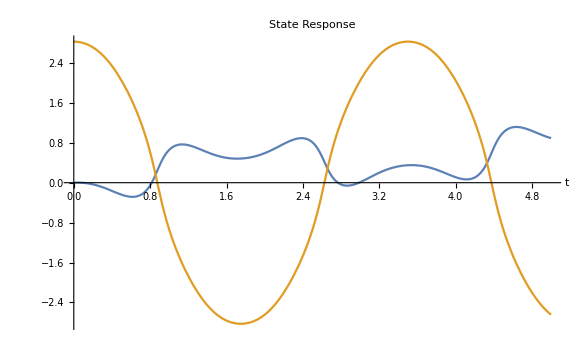

```mathematica
Plot[resp,{t,0,5},PlotLabel->"State Response",AxesLabel->Automatic]
```

```mathematica
res = OutputResponse[{csys/.pars,{85,0,-3,0}},0,{t,0,10}]
```

{InterpolatingFunction[{{0., 10.}}, <>][t],InterpolatingFunction[{{0., 10.}}, <>][t]}

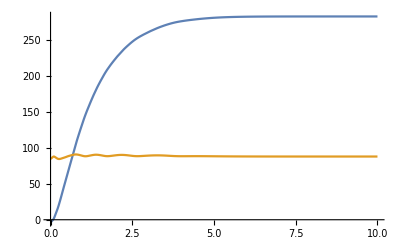

```mathematica
Plot[res,{t,0,10}]
```